# Analysis of surface profiles taken using the Keyence microscope in the microfluidics lab

Last updated 06/01/16 by Leanne Friedrich
This program requires inputs of .csv files taken from surface profiles, where the printed line goes from left to right

```mathematica
SetDirectory[NotebookDirectory[]];
<<Functions_k.wl;
```

List of keyence files, by date

```mathematica
Grid[SortBy[{#, DateString[FileDate[#]]}&/@kFiles, #[[2]]&]]
```

## Analyze

run code

This code will analyze keyence csv files, stored in kFiles between index startingIndex and finishingIndex, and print out error messages if there are any.

```mathematica
startingIndex = 1;
finishingIndex = 1247;
Do[If[Mod[i, 25]==0, Print[i]];blah = Check[getWidthHeight[kFiles[[i]]]; ,i]; If[blah≠0, Print[blah]];, {i,startingIndex, finishingIndex}]
```

check your work

Check if your analysis worked by looking at the line profiles. If there are problems, you will need to go into the source code and fix them.

```mathematica
profiles = FileNames["*K*profile.tiff", basedir, Infinity];
Length[profiles]
```

1249

```mathematica
Row[Table[Column[{i, FileNameSplit[profiles[[i]]][[-1]],FileNameSplit[kFiles[[i]]][[-1]], Show[Import[profiles[[i]]], ImageSize->200]}, Frame->True],{i,1, 25}]]
```

1
K_LF26_SiO5_A24_CSph120_V0_L13_1_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L13_1.csv
-Graphics-2
K_LF26_SiO5_A24_CSph120_V0_L13_2_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L13_2.csv
-Graphics-3
K_LF26_SiO5_A24_CSph120_V0_L5_1_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L5_1.csv
-Graphics-4
K_LF26_SiO5_A24_CSph120_V0_L5_2_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L5_2.csv
-Graphics-5
K_LF26_SiO5_A24_CSph120_V0_L3_1_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L3_1.csv
-Graphics-6
K_LF26_SiO5_A24_CSph120_V0_L3_2_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L3_2.csv
-Graphics-7
K_LF26_SiO5_A24_CSph120_V0_L8_1_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L8_1.csv
-Graphics-8
K_LF26_SiO5_A24_CSph120_V0_L8_2_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L8_2.csv
-Graphics-9
K_LF26_SiO5_A24_CSph120_V0_L9_1_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L9_1.csv
-Graphics-10
K_LF26_SiO5_A24_CSph120_V0_L9_2_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L9_2.csv
-Graphics-11
K_LF26_SiO5_A24_CSph120_V0_L6_1_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L6_1.csv
-Graphics-12
K_LF26_SiO5_A24_CSph120_V0_L6_2_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L6_2.csv
-Graphics-13
K_LF26_SiO5_A24_CSph120_V0_L7_1_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L7_1.csv
-Graphics-14
K_LF26_SiO5_A24_CSph120_V0_L7_2_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L7_2.csv
-Graphics-15
K_LF26_SiO5_A24_CSph120_V0_L10_1_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L10_1.csv
-Graphics-16
K_LF26_SiO5_A24_CSph120_V0_L10_2_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L10_2.csv
-Graphics-17
K_LF26_SiO5_A24_CSph120_V0_L11_1_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L11_1.csv
-Graphics-18
K_LF26_SiO5_A24_CSph120_V0_L11_2_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L11_2.csv
-Graphics-19
K_LF26_SiO5_A24_CSph120_V0_L12_1_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L12_1.csv
-Graphics-20
K_LF26_SiO5_A24_CSph120_V0_L12_2_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L12_2.csv
-Graphics-21
K_LF26_SiO5_A24_CSph120_V0_L4_1_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L4_1.csv
-Graphics-22
K_LF26_SiO5_A24_CSph120_V0_L4_2_profile.tiff
K_LF26_SiO5_A24_CSph120_V0_L4_2.csv
-Graphics-23
K_LF26_SiO5_A24_CSph120_V15_L3_1_profile.tiff
K_LF26_SiO5_A24_CSph120_V15_L3_1.csv
-Graphics-24
K_LF26_SiO5_A24_CSph120_V15_L3_2_profile.tiff
K_LF26_SiO5_A24_CSph120_V15_L3_2.csv
-Graphics-25
K_LF26_SiO5_A24_CSph120_V15_L4_1_profile.tiff
K_LF26_SiO5_A24_CSph120_V15_L4_1.csv
-Graphics-

## Old stuff

#### View derivatives

```mathematica
Manipulate[
l = Mean@Transpose@Import[kFiles[[fileIndex]], "csv"][[10;;1190, 400;;1200]];
l2 = getderivatives[l, m];
Column[ListPlot[#, PlotStyle->Black, ImageSize->Medium]&/@l2[[2;;3]]], {m, 10, 20,1}, {{fileIndex,50}, 1, Length[kFiles]} ]
```

#### Get Widths and Heights

This is from an older version

```mathematica
index = 763;
kFiles[[index]]
profiles[[index-1]]
getWidthHeight[kFiles[[index]]]
Import[profiles[[index-1]]]
```

```mathematica
1227-1061+942
```

1108

```mathematica
ppp = Import[FileNames["*K_LF66_SiO9_A8_CSph700_V25_L6_2_allprofs*", "*", Infinity][[1]]];
```

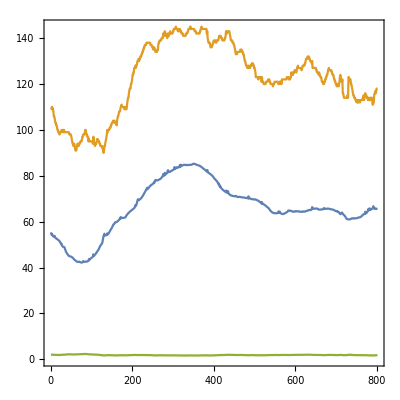

```mathematica
ListLinePlot[{ppp[[1;;-3,1]],ppp[[1;;-3,4]], ppp[[1;;-3,5]]}]
```